# Mathematica for Bioinformatics

by George I. Mias, PhD
["http://georgemias.org"](http://georgemias.org)

Cite this chapter as:
Mias G. (2018) Machine Learning. In: Mathematica for Bioinformatics. Springer, Cham. https://doi.org/10.1007/978-3-319-72377-8_9

## Chapter 9: Machine Learning

## A taste of clustering

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
golubAssociation=<<"golubAssociation";
```

```mathematica
hu6800IDtoAnnotation=<<"hu6800IDtoAnnotation";
```

```mathematica
myosinExample=Query[All,"M31211_s_at"]@golubAssociation
```

<|AML→{-0.929698,-1.21439,-1.36559,-1.03054,-1.29915,-0.401122,-0.263245,-1.27241,-0.651176,-0.323125,-1.43473,-0.203518,-1.04336,-1.22702,-1.28071,0.260207,-1.05801,-0.720331,-0.809905,-0.588208,-0.513632,-0.247296,-1.42036,-1.48163,-1.3111},ALL→{0.21673,-0.0512012,0.0512196,0.0658298,0.355842,-0.0764156,-0.298932,-0.46567,0.490372,0.651373,0.715212,0.148149,0.354363,-0.466193,0.576175,0.417461,-0.407586,0.388138,0.266817,0.634913,0.707898,-0.775871,0.0765331,0.108658,0.224704,0.466898,-0.87136,0.193097,-0.37865,-0.0896119,0.284866,0.51995,-0.204948,0.560927,-0.0758743,0.726773,0.337038,0.374954,0.146782,-0.474574,0.170777,0.136991,0.107438,-0.55069,0.279121,-0.665758,0.545882}|>

```mathematica
labelsMYL6BAML=Thread[#-> "AML"&@Range[1,25]]
```

{1→AML,2→AML,3→AML,4→AML,5→AML,6→AML,7→AML,8→AML,9→AML,10→AML,11→AML,12→AML,13→AML,14→AML,15→AML,16→AML,17→AML,18→AML,19→AML,20→AML,21→AML,22→AML,23→AML,24→AML,25→AML}

```mathematica
labelsMYL6BALL=Thread[#-> "ALL"&@Range[1,47]]
```

{1→ALL,2→ALL,3→ALL,4→ALL,5→ALL,6→ALL,7→ALL,8→ALL,9→ALL,10→ALL,11→ALL,12→ALL,13→ALL,14→ALL,15→ALL,16→ALL,17→ALL,18→ALL,19→ALL,20→ALL,21→ALL,22→ALL,23→ALL,24→ALL,25→ALL,26→ALL,27→ALL,28→ALL,29→ALL,30→ALL,31→ALL,32→ALL,33→ALL,34→ALL,35→ALL,36→ALL,37→ALL,38→ALL,39→ALL,40→ALL,41→ALL,42→ALL,43→ALL,44→ALL,45→ALL,46→ALL,47→ALL}

```mathematica
?FindClusters
```

```mathematica
Flatten@Values@myosinExample-> Values@Join[labelsMYL6BAML,labelsMYL6BALL]//Short
```

{-0.929698,«70»,0.545882}→«1»

```mathematica
FindClusters[Flatten@Values@myosinExample->Join[labelsMYL6BAML,labelsMYL6BALL]]
```

{{1→AML,2→AML,3→AML,4→AML,5→AML,8→AML,11→AML,13→AML,14→AML,15→AML,17→AML,23→AML,24→AML,25→AML},{6→AML,7→AML,9→AML,10→AML,12→AML,18→AML,19→AML,20→AML,21→AML,22→AML,7→ALL,8→ALL,14→ALL,17→ALL,22→ALL,27→ALL,29→ALL,33→ALL,40→ALL,44→ALL,46→ALL},{16→AML,1→ALL,2→ALL,3→ALL,4→ALL,5→ALL,6→ALL,9→ALL,10→ALL,11→ALL,12→ALL,13→ALL,15→ALL,16→ALL,18→ALL,19→ALL,20→ALL,21→ALL,23→ALL,24→ALL,25→ALL,26→ALL,28→ALL,30→ALL,31→ALL,32→ALL,34→ALL,35→ALL,36→ALL,37→ALL,38→ALL,39→ALL,41→ALL,42→ALL,43→ALL,45→ALL,47→ALL}}

```mathematica
Counts[Values@#]&/@%
```

{<|AML→14|>,<|AML→10,ALL→11|>,<|AML→1,ALL→36|>}

## Dimensional Reduction

```mathematica
golubOmicsObject=<<golubOmicsObject;
```

```mathematica
golubPhenotypeData=<<golubPhenotypeData;
```

```mathematica
golubPhenotypeData//Short
```

<|Samples→{ALL/AML,«8»,Source},«71»,72→{«1»}|>

```mathematica
sampleToCondition=Query[2;;,1]@golubPhenotypeData;
sampleToCondition//Short
```

<|1→ALL,2→ALL,«68»,71→ALL,72→ALL|>

```mathematica
genesAllGolub=#[[2]]-> sampleToCondition[#[[1]]]&/@Normal@Query[All,Values/*Flatten]@golubOmicsObject;
```

```mathematica
genesAllGolub[[1]]//Short[#,3]&
```

{-0.78835,-0.756913,«3567»,-0.331179,-0.825661}→ALL

```mathematica
golub2Dimensions=DimensionReduce[Keys@genesAllGolub,2,Method->"PrincipalComponentsAnalysis"];
```

```mathematica
golub2Dimensions//Short[#,5]&
```

{{4.25183,23.2184},{-7.23657,-8.71078},«68»,{35.1694,14.8217},{11.9888,-15.5859}}

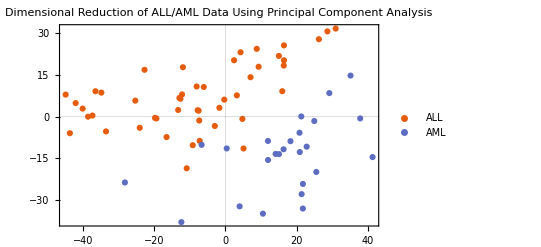

```mathematica
golubByDisease=GroupBy[Thread[golub2Dimensions->
Values@genesAllGolub],Last->First];
ListPlot[Values[golubByDisease],
PlotLegends->Keys[golubByDisease],
PlotTheme->"Scientific",
PlotLabel-> 
"Dimensional Reduction of ALL/AML Data
Using Principal Component Analysis"]
```

```mathematica
golub2DimensionsTSNE=DimensionReduce[Keys@genesAllGolub,2,Method->"TSNE"];
```

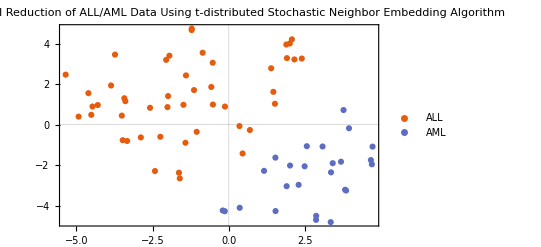

```mathematica
golubByDiseaseTSNE=GroupBy[Thread[golub2DimensionsTSNE->Values@genesAllGolub],Last->First];
ListPlot[Values[golubByDiseaseTSNE],
PlotLegends->Keys[golubByDiseaseTSNE],
PlotTheme->"Scientific",
PlotLabel-> 
"Dimensional Reduction of ALL/AML Data
Using t-distributed Stochastic Neighbor Embedding Algorithm"]
```

## Classification

```mathematica
SeedRandom[3333];
randomGolub=RandomSample[genesAllGolub];
```

```mathematica
trainGolub=randomGolub[[1;;51]];
testGolub=randomGolub[[52;;]];
```

```mathematica
golubClassifier= Classify[trainGolub,Method->"LogisticRegression"];
```

```mathematica
Head@golubClassifier
```

ClassifierFunction

```mathematica
testGolub[[1]]//Short[#,5]&
```

{-1.31426,-1.31426,-1.31426,-0.772743,«3563»,-1.01648,0.603772,0.238744,-0.221022}→AML

```mathematica
golubClassifier[testGolub[[1,1]]]
```

AML

```mathematica
golubClassifier[testGolub[[1,1]],"Properties"]
```

{Decision,Distribution,ExpectedUtilities,LogProbabilities,Probabilities,Properties,RarerProbability,SHAPValues,TopProbabilities}

```mathematica
golubClassifier[testGolub[[1,1]],"Probabilities"]
```

<|ALL→4.24138×10^-16,AML→1.|>

```mathematica
ClassifierMeasurements[golubClassifier,testGolub,"Accuracy"]
```

0.952381

```mathematica
ClassifierMeasurements[golubClassifier,testGolub,"ConfusionMatrix"]
```

{{14,1,0},{0,6,0}}

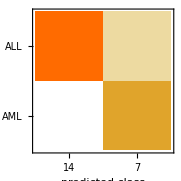

```mathematica
ClassifierMeasurements[golubClassifier,testGolub,"ConfusionMatrixPlot"]
```

## The Iris Data Classified Across Methods

```mathematica
ExampleData["MachineLearning"]
```

{{MachineLearning,BostonHomes},{MachineLearning,FisherIris},{MachineLearning,MNIST},{MachineLearning,MovieReview},{MachineLearning,Mushroom},{MachineLearning,Satellite},{MachineLearning,Titanic},{MachineLearning,UCILetter},{MachineLearning,WineQuality}}

```mathematica
ExampleData[{"MachineLearning","FisherIris"},"Properties"]
```

{Data,Description,Data,Dimensions,LearningTask,LongDescription,MissingData,Name,Source,TestData,TrainingData,VariableDescriptions,VariableTypes}

```mathematica
ExampleData[{"MachineLearning","FisherIris"},"Source"]
```

Fisher,R.A. "The use of multiple measurements in taxonomic problems" Annual Eugenics, 7, Part II, 179-188 (1936); 
also in "Contributions to Mathematical Statistics" (John Wiley, NY, 1950).

```mathematica
ExampleData[{"MachineLearning","FisherIris"},"LongDescription"]
```

The data set consists of 50 samples from each of three species of iris flowers (setosa, versicolor and virginica). Four features were measured from each flower, 
	the length and the width of the sepal and petal.

	The test and training sets were constructed by stratified random sampling, using 30% of the data for the test set and the rest for the training set.

```mathematica
ExampleData[{"MachineLearning","FisherIris"},"Dimensions"]
```

<|NumberClasses→3,NumberFeatures→4,NumberExamples→150|>

Iris

WolframAlphaQueryResults

```mathematica
irisData=ExampleData[{"MachineLearning","FisherIris"},"Data"];
```

```mathematica
irisData[[1;;3]]
```

{{5.1,3.5,1.4,0.2}→setosa,{4.9,3.,1.4,0.2}→setosa,{4.7,3.2,1.3,0.2}→setosa}

```mathematica
ExampleData[{"MachineLearning","FisherIris"},"VariableDescriptions"]
```

{Sepal length in cm.,Sepal width in cm.,Petal length in cm.,Petal width in cm.,Species of iris}→species of iris

```mathematica
SeedRandom[7777];
randomIris=RandomSample[irisData];
```

```mathematica
randomIris//Short[#,5]&
```

{{6.4,2.8,5.6,2.1}→virginica,{5.,3.6,1.4,0.2}→setosa,{7.2,3.6,6.1,2.5}→virginica,«145»,{5.4,3.,4.5,1.5}→versicolor,{7.1,3.,5.9,2.1}→virginica}

```mathematica
trainIris=randomIris[[1;;105]];
testIris=randomIris[[106;;]];
```

```mathematica
classifyMethods={"DecisionTree","GradientBoostedTrees","LogisticRegression","Markov","NaiveBayes","NearestNeighbors","NeuralNetwork","RandomForest","SupportVectorMachine"};
```

```mathematica
trainIrisClassifiers=Association@@(#-> Classify[trainIris,Method->{#}]&/@classifyMethods)
```

<|DecisionTree→ClassifierFunction[…],GradientBoostedTrees→ClassifierFunction[…],LogisticRegression→ClassifierFunction[…],Markov→ClassifierFunction[…],NaiveBayes→ClassifierFunction[…],NearestNeighbors→ClassifierFunction[…],NeuralNetwork→ClassifierFunction[…],RandomForest→ClassifierFunction[…],SupportVectorMachine→ClassifierFunction[…]|>

```mathematica
testIris[[4]]
```

{6.1,2.9,4.7,1.4}→versicolor

```mathematica
Query[All,#[{6.1,2.9,4.7,1.4}]&]@trainIrisClassifiers
```

<|DecisionTree→versicolor,GradientBoostedTrees→versicolor,LogisticRegression→versicolor,Markov→versicolor,NaiveBayes→versicolor,NearestNeighbors→versicolor,NeuralNetwork→versicolor,RandomForest→versicolor,SupportVectorMachine→versicolor|>

```mathematica
Query[All,ClassifierMeasurements[#,testIris,"Accuracy"]&]@trainIrisClassifiers
```

<|DecisionTree→0.866667,GradientBoostedTrees→0.933333,LogisticRegression→0.977778,Markov→0.866667,NaiveBayes→0.933333,NearestNeighbors→0.955556,NeuralNetwork→0.977778,RandomForest→0.933333,SupportVectorMachine→0.955556|>

```mathematica
Query[All,ClassifierMeasurements[#,testIris,"ConfusionMatrix"]&]@trainIrisClassifiers
```

<|DecisionTree→{{11,4,0,0},{0,13,2,0},{0,0,15,0}},GradientBoostedTrees→{{15,0,0,0},{0,13,2,0},{0,1,14,0}},LogisticRegression→{{15,0,0,0},{0,15,0,0},{0,1,14,0}},Markov→{{15,0,0,0},{0,10,5,0},{0,1,14,0}},NaiveBayes→{{15,0,0,0},{2,12,1,0},{0,0,15,0}},NearestNeighbors→{{15,0,0,0},{0,14,1,0},{0,1,14,0}},NeuralNetwork→{{15,0,0,0},{0,14,1,0},{0,0,15,0}},RandomForest→{{14,1,0,0},{0,13,2,0},{0,0,15,0}},SupportVectorMachine→{{15,0,0,0},{0,15,0,0},{0,2,13,0}}|>

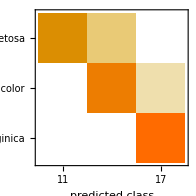
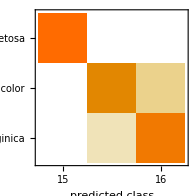
<|DecisionTree→-Graphics-,GradientBoostedTrees→-Graphics-|>

```mathematica
Query[1;;2,ClassifierMeasurements[#,testIris,"ConfusionMatrixPlot"]&]@trainIrisClassifiers
```